```mathematica
ListCPU = {0.0073891, 0.0590191, 0.202167, 0.484104, 0.970289, 1.72743, 2.8821, 4.54137, 7.39637,11.0832, 15.4828, 17.4476, 26.4612, 33.0516, 42.3598, 49.4399, 61.4617, 72.8836,86.2271, 87.499};
ListGPU = {1.31072*10^-4, 1.65312*10^-4, 5.69056*10^-4 , 0.001031, 0.00247075, 0.00423456, 0.0121385, 0.0345057,0.0465654, 0.0618557, 0.0826378, 0.074197, 0.095452, 0.1179, 0.142792, 0.185839, 0.212458,0.249434, 0.297014, 0.303333};
```

```mathematica
us = ListCPU/ListGPU
```

{56.3744,357.016,355.267,469.548,392.71,407.936,237.435,131.612,158.838,179.178,187.357,235.152,277.22,280.336,296.654,266.036,289.289,292.196,290.313,288.459}

```mathematica
a = Fit[ListCPU,{1,x,x^2},x]
```

5.70111-3.21896 x+0.37757 x^2

```mathematica
b= Fit[ListGPU,{1,x,x^2},x]
```

0.00969313-0.00680628 x+0.00110111 x^2

```mathematica
mf=Function[{x,y},Evaluate@D[Sin[Sqrt[2] x]+Sin[x],x]];
```

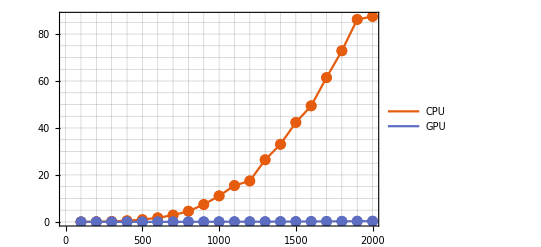

```mathematica
ListLinePlot[{ListCPU, ListGPU},DataRange->{100,2000}, GridLines->{{0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000},{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90}},PlotLegends->{"CPU","GPU"},Mesh->Full, PlotTheme->"Scientific"]
```

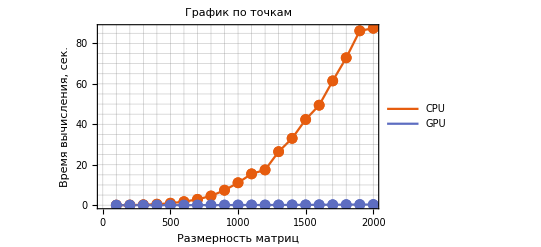

```mathematica
Show[%124,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Время"," ","вычисления"}],","," ",RowBox[{"сек","."}]}]],None},{HoldForm[Размерность матриц],None}},PlotLabel->HoldForm[График по точкам],LabelStyle->{11,GrayLevel[0]}]
```

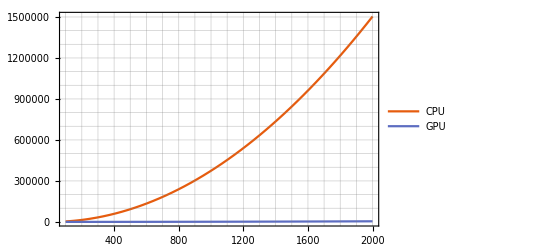

```mathematica
Show[{Plot[{a,b},{x,100,2000}, GridLines->{{0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000},{100000,200000,3*10^5,4*10^5,5*10^5,6*10^5,7*10^5,8*10^5,9*10^5,10*10^5,11*10^5,12*10^5,13*10^5,14*10^5,15*10^5}},PlotLegends->{"CPU","GPU"}, PlotTheme->"Scientific"],ListPlot[{ListCPU,ListGPU}]}]
```

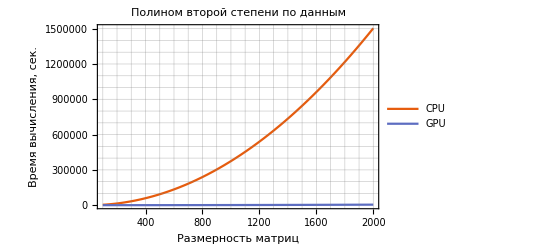

```mathematica
Show[%5,FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Время"," ","вычисления"}],","," ",RowBox[{"сек","."}]}]],None},{HoldForm[Размерность матриц],None}},PlotLabel->HoldForm[Полином второй степени по данным],LabelStyle->{11,GrayLevel[0]}]
```